# Effet Stark

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from Publica
tion T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.131145,2.65486,2.64165,1.34807,1.34642, 0.0165192,0.0165437,0};
Subscript[δ, 2]={0.195,0.280,0.318,-0.603,-0.545, -0.085,-0.086,0}; (*Meschede values*)

(*Subscript[δ, 0]={3.131804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};*)
(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)
```

0.0164925

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Desktop\radinte\radinte.exe",25,10]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

0.026683

0.026683

-0.00761042

{0.,-0.00762856}

1.

1.

-5.83172×10^-6

1.

-4.42004×10^-6

2

4/3

0.00139962

0.00279925

## | 60 p3/2 >

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=60;Subscript[l, 1]=1;Subscript[j, 1]=3/2;Subscript[m, 1]=3/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=50; Subscript[n, max]=70;

lmax = 4;
δf=40*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤lmax ,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]
]]
]
Length[NList]

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
NList
```

-9.99955×10^11

{0.016,Null}

106

{{57,3,5/2,-5/2,-1.01315×10^12,-1},{57,3,5/2,-3/2,-1.01315×10^12,-1},{57,3,5/2,-1/2,-1.01315×10^12,-1},{57,3,5/2,1/2,-1.01315×10^12,-1},{57,3,5/2,3/2,-1.01315×10^12,-1},{57,3,5/2,5/2,-1.01315×10^12,-1},{57,3,7/2,-7/2,-1.01315×10^12,-1},{57,3,7/2,-5/2,-1.01315×10^12,-1},{57,3,7/2,-3/2,-1.01315×10^12,-1},{57,3,7/2,-1/2,-1.01315×10^12,-1},{57,3,7/2,1/2,-1.01315×10^12,-1},{57,3,7/2,3/2,-1.01315×10^12,-1},{57,3,7/2,5/2,-1.01315×10^12,-1},{57,3,7/2,7/2,-1.01315×10^12,-1},{57,4,7/2,-7/2,-1.01256×10^12,1},{57,4,7/2,-5/2,-1.01256×10^12,1},{57,4,7/2,-3/2,-1.01256×10^12,1},{57,4,7/2,-1/2,-1.01256×10^12,1},{57,4,7/2,1/2,-1.01256×10^12,1},{57,4,7/2,3/2,-1.01256×10^12,1},{57,4,7/2,5/2,-1.01256×10^12,1},{57,4,7/2,7/2,-1.01256×10^12,1},{57,4,9/2,-9/2,-1.01256×10^12,1},{57,4,9/2,-7/2,-1.01256×10^12,1},{57,4,9/2,-5/2,-1.01256×10^12,1},{57,4,9/2,-3/2,-1.01256×10^12,1},{57,4,9/2,-1/2,-1.01256×10^12,1},{57,4,9/2,1/2,-1.01256×10^12,1},{57,4,9/2,3/2,-1.01256×10^12,1},{57,4,9/2,5/2,-1.01256×10^12,1},{57,4,9/2,7/2,-1.01256×10^12,1},{57,4,9/2,9/2,-1.01256×10^12,1},{58,2,3/2,-3/2,-1.02504×10^12,1},{58,2,3/2,-1/2,-1.02504×10^12,1},{58,2,3/2,1/2,-1.02504×10^12,1},{58,2,3/2,3/2,-1.02504×10^12,1},{58,2,5/2,-5/2,-1.02498×10^12,1},{58,2,5/2,-3/2,-1.02498×10^12,1},{58,2,5/2,-1/2,-1.02498×10^12,1},{58,2,5/2,1/2,-1.02498×10^12,1},{58,2,5/2,3/2,-1.02498×10^12,1},{58,2,5/2,5/2,-1.02498×10^12,1},{58,3,5/2,-5/2,-9.78506×10^11,-1},{58,3,5/2,-3/2,-9.78506×10^11,-1},{58,3,5/2,-1/2,-9.78506×10^11,-1},{58,3,5/2,1/2,-9.78506×10^11,-1},{58,3,5/2,3/2,-9.78506×10^11,-1},{58,3,5/2,5/2,-9.78506×10^11,-1},{58,3,7/2,-7/2,-9.78506×10^11,-1},{58,3,7/2,-5/2,-9.78506×10^11,-1},{58,3,7/2,-3/2,-9.78506×10^11,-1},{58,3,7/2,-1/2,-9.78506×10^11,-1},{58,3,7/2,1/2,-9.78506×10^11,-1},{58,3,7/2,3/2,-9.78506×10^11,-1},{58,3,7/2,5/2,-9.78506×10^11,-1},{58,3,7/2,7/2,-9.78506×10^11,-1},{58,4,7/2,-7/2,-9.77949×10^11,1},{58,4,7/2,-5/2,-9.77949×10^11,1},{58,4,7/2,-3/2,-9.77949×10^11,1},{58,4,7/2,-1/2,-9.77949×10^11,1},{58,4,7/2,1/2,-9.77949×10^11,1},{58,4,7/2,3/2,-9.77949×10^11,1},{58,4,7/2,5/2,-9.77949×10^11,1},{58,4,7/2,7/2,-9.77949×10^11,1},{58,4,9/2,-9/2,-9.77949×10^11,1},{58,4,9/2,-7/2,-9.77949×10^11,1},{58,4,9/2,-5/2,-9.77949×10^11,1},{58,4,9/2,-3/2,-9.77949×10^11,1},{58,4,9/2,-1/2,-9.77949×10^11,1},{58,4,9/2,1/2,-9.77949×10^11,1},{58,4,9/2,3/2,-9.77949×10^11,1},{58,4,9/2,5/2,-9.77949×10^11,1},{58,4,9/2,7/2,-9.77949×10^11,1},{58,4,9/2,9/2,-9.77949×10^11,1},{59,1,1/2,-1/2,-1.03624×10^12,-1},{59,1,1/2,1/2,-1.03624×10^12,-1},{59,1,3/2,-3/2,-1.03576×10^12,-1},{59,1,3/2,-1/2,-1.03576×10^12,-1},{59,1,3/2,1/2,-1.03576×10^12,-1},{59,1,3/2,3/2,-1.03576×10^12,-1},{59,2,3/2,-3/2,-9.89787×10^11,1},{59,2,3/2,-1/2,-9.89787×10^11,1},{59,2,3/2,1/2,-9.89787×10^11,1},{59,2,3/2,3/2,-9.89787×10^11,1},{59,2,5/2,-5/2,-9.89731×10^11,1},{59,2,5/2,-3/2,-9.89731×10^11,1},{59,2,5/2,-1/2,-9.89731×10^11,1},{59,2,5/2,1/2,-9.89731×10^11,1},{59,2,5/2,3/2,-9.89731×10^11,1},{59,2,5/2,5/2,-9.89731×10^11,1},{60,0,1/2,-1/2,-1.01724×10^12,1},{60,0,1/2,1/2,-1.01724×10^12,1},{60,1,1/2,-1/2,-1.00042×10^12,-1},{60,1,1/2,1/2,-1.00042×10^12,-1},{60,1,3/2,-3/2,-9.99955×10^11,-1},{60,1,3/2,-1/2,-9.99955×10^11,-1},{60,1,3/2,1/2,-9.99955×10^11,-1},{60,1,3/2,3/2,-9.99955×10^11,-1},{61,0,1/2,-1/2,-9.82389×10^11,1},{61,0,1/2,1/2,-9.82389×10^11,1},{61,1,1/2,-1/2,-9.66416×10^11,-1},{61,1,1/2,1/2,-9.66416×10^11,-1},{61,1,3/2,-3/2,-9.65979×10^11,-1},{61,1,3/2,-1/2,-9.65979×10^11,-1},{61,1,3/2,1/2,-9.65979×10^11,-1},{61,1,3/2,3/2,-9.65979×10^11,-1}}

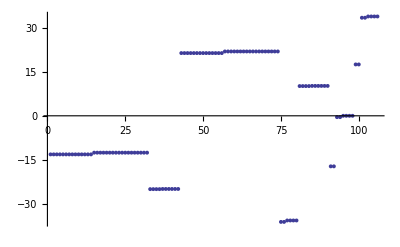

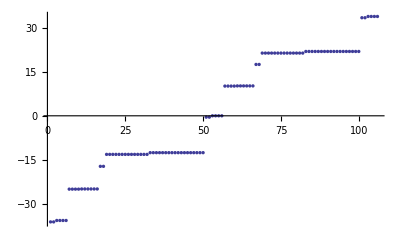

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
Calcul des éléments de matrice non-diagonaux
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);



EMatrixelement[{60,0,1/2,1/2},{58,1,1/2,-1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]
```

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{160.399,0.-160.399 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{7/2, -7/2}, {1, -1}, {5/2, 5/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, -7/2}, {1, 0}, {5/2, 5/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -7/2}, {1, -1}, {5/2, 5/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -7/2}, {1, 1}, {5/2, 5/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -7/2}, {1, -1}, {5/2, 5/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{6.521,Null}

## Zeeman effect

1.

1.

-5.83172×10^-6

1.

-4.42004×10^-6

2

4/3

0.00139962

0.00279925

{0.281,Null}

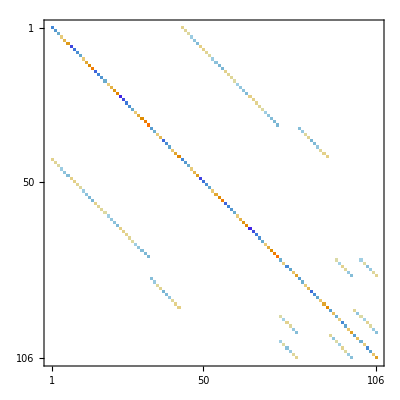

```mathematica
αB=0;
(*Calculation of Zeeman term <n,l,j,m| μ*B |np,lp,jp,mp> *)


RZeeman [{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,0];
RZeeman [{60,0,1},{60,0,1}]
RZeeman [{100,0,1},{100,0,1}]
RZeeman [{60,0,1},{59,0,1}]
RZeeman [{60,1,3},{60,1,3}]
RZeeman [{60,1,3},{59,1,3}]

(*Landé g-factor*)
g[l_,j_] := 3/2+(3/4-l*(l+1))/(2*j*(j+1));

g[0,1/2]
g[1,3/2]
BMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_},α_]:=RZeeman [{np,lp,Chooselj[lp,jp]},{n,l,Chooselj[l,j]}]  *  g[lp,jp]* KroneckerDelta[lp,l]*KroneckerDelta[jp,j]* (Cos[α]*mp*KroneckerDelta[mp,m]+Sin[α]/2*(Sqrt[jp*(jp+1)-mp*(mp+1)]*KroneckerDelta[mp+1,m]+Sqrt[jp*(jp+1)-mp*(mp-1)]*KroneckerDelta[mp-1,m])  );

BMatrixelement[{60,0,1/2,1/2},{60,0,1/2,1/2},0]*Subscript[μ, B]/h/10^9*10^(-4) (*Zeeman effect, GHz per Gauss, for s fine levels *)
BMatrixelement[{60,1,3/2,3/2},{60,1,3/2,3/2},0]*Subscript[μ, B]/h/10^9*10^(-4)  (*Zeeman effect, GHz per Gauss, for p 3/2 fine levels *)


(*Fill up Matrix with  <A|μ*B|A'>  *)
Clear[AI]
BMatrix=Array[B,{Length[NList],Length[NList]}];
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[ (NList[[i,2]]==NList[[k,2]])&&(NList[[i,3]]==NList[[k,3]]) ,
BMatrix[[i,k]]=BMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]},αB],
BMatrix[[i,k]]=0;]]
] 
] 

Clear[i,k,AI]

MatrixPlot[BMatrix]
```

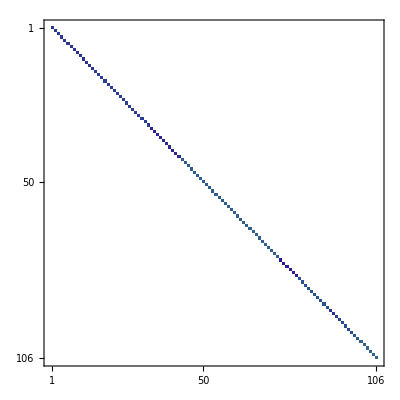

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

{{{100,-37.1164}},{{100,-37.1164}},{{100,-36.5728}},{{100,-36.5728}},{{100,-36.3677}},{{100,-36.3677}},{{100,-25.4471}},{{100,-25.4471}},{{100,-25.4005}},{{100,-25.4005}},{{100,-25.2304}},{{100,-25.2304}},{{100,-25.1619}},{{100,-25.1619}},{{100,-25.122}},{{100,-25.122}},{{100,-17.3886}},{{100,-17.3886}},{{100,-15.6831}},{{100,-15.6831}},{{100,-15.63}},{{100,-15.63}},{{100,-15.6283}},{{100,-15.6283}},{{100,-15.4403}},{{100,-15.4403}},{{100,-15.4387}},{{100,-15.4387}},{{100,-15.0038}},{{100,-15.0038}},{{100,-15.0034}},{{100,-15.0034}},{{100,-12.6092}},{{100,-12.6092}},{{100,-12.6092}},{{100,-12.6092}},{{100,-10.8139}},{{100,-10.8139}},{{100,-10.8136}},{{100,-10.8136}},{{100,-10.0849}},{{100,-10.0849}},{{100,-10.0841}},{{100,-10.0841}},{{100,-9.71071}},{{100,-9.71071}},{{100,-9.70993}},{{100,-9.70993}},{{100,-9.59286}},{{100,-9.59286}},{{100,-1.00641}},{{100,-1.00641}},{{100,-0.6326}},{{100,-0.6326}},{{100,-0.554826}},{{100,-0.554826}},{{100,9.83008}},{{100,9.83008}},{{100,9.87286}},{{100,9.87286}},{{100,10.1291}},{{100,10.1291}},{{100,10.1911}},{{100,10.1911}},{{100,10.2609}},{{100,10.2609}},{{100,17.4827}},{{100,17.4827}},{{100,18.9738}},{{100,18.9738}},{{100,19.0182}},{{100,19.0182}},{{100,19.0201}},{{100,19.0201}},{{100,19.1806}},{{100,19.1806}},{{100,19.1821}},{{100,19.1821}},{{100,19.5674}},{{100,19.5674}},{{100,19.5678}},{{100,19.5678}},{{100,22.0058}},{{100,22.0058}},{{100,22.0058}},{{100,22.0058}},{{100,23.8991}},{{100,23.8991}},{{100,23.8994}},{{100,23.8994}},{{100,24.7166}},{{100,24.7166}},{{100,24.7172}},{{100,24.7172}},{{100,25.141}},{{100,25.141}},{{100,25.1419}},{{100,25.1419}},{{100,25.2753}},{{100,25.2753}},{{100,33.7332}},{{100,33.7332}},{{100,34.0736}},{{100,34.0736}},{{100,34.503}},{{100,34.503}}}

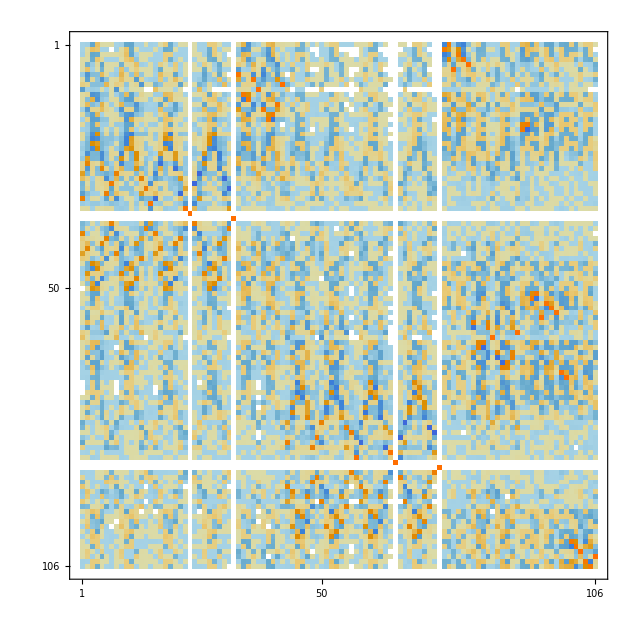

Part::partw: Part 112 of {{-1.69825×10^-15, -1.35949×10^-14, -0.0103719, 0.0219849, 1.05774×10^-14, 1.77319×10^-15, 3.46393×10^-15, -7.50041×10^-16, -1.56724×10^-14, -0.00555646, -0.0117778, -6.74923×10^-15, -3.96985×10^-15, 1.70019×10^-15, -1.14213×10^-14, -7.32797×10^-16, « 20 », -1.60915×10^-15, 3.34844×10^-14, 0.0475145, 0.100715, 1.40411×10^-13, 3.74061×10^-14, 6.85611×10^-15, 9.91501×10^-16, 0.0000820664, -0.000173953, 2.89618×10^-15, -6.04534×10^-15, 1.2915×10^-15, -3.05435×10^-16, « 56 »}, {« 1 »}, « 47 », {« 1 »}, « 56 »} does not exist.

ListPlot::lpn: {{-1.69825×10^-15, -1.35949×10^-14, -0.0103719, 0.0219849, 1.05774×10^-14, 1.77319×10^-15, 3.46393×10^-15, -7.50041×10^-16, -1.56724×10^-14, -0.00555646, -0.0117778, -6.74923×10^-15, -3.96985×10^-15, 1.70019×10^-15, -1.14213×10^-14, -7.32797×10^-16, « 20 », -1.60915×10^-15, 3.34844×10^-14, 0.0475145, 0.100715, 1.40411×10^-13, 3.74061×10^-14, 6.85611×10^-15, 9.91501×10^-16, 0.0000820664, -0.000173953, 2.89618×10^-15, -6.04534×10^-15, 1.2915×10^-15, -3.05435×10^-16, « 56 »}, « 49 », « 56 »} ⟦ 112 ⟧ is not a list of numbers or pairs of numbers.

ListPlot[{{-1.69825×10^-15,-1.35949×10^-14,-0.0103719,0.0219849,1.05774×10^-14,1.77319×10^-15,3.46393×10^-15,-7.50041×10^-16,-1.56724×10^-14,-0.00555646,-0.0117778,-6.74923×10^-15,-3.96985×10^-15,1.70019×10^-15,-1.14213×10^-14,«76»,0.103043,-0.00573909,0.0121649,-5.28756×10^-16,-0.00533127,-0.0113005,-7.76009×10^-15,-0.00214454,-0.0045457,0.000602293,-0.00127666,7.84155×10^-15,0.00055171,0.00116944,6.40334×10^-16},«104»,{-«23»,«104»,«23»}}⟦112⟧,«1»]

{{{100,-37.6879}},{{100,-37.6484}},{{100,-37.4523}},{{100,-37.4222}},{{100,-37.2225}},{{100,-37.1976}},{{100,-37.1306}},{{100,-36.995}},{{100,-36.9738}},{{100,-36.7692}},{{100,-36.7506}},{{100,-36.5444}},{{100,-36.5279}},{{100,-36.3203}},{{100,-36.3056}},{{100,-36.0968}},{{100,-36.0835}},{{100,-35.8737}},{{100,-35.8617}},{{100,-35.6509}},{{100,-35.6401}},{{100,-35.4284}},{{100,-35.4186}},{{100,-35.2061}},{{100,-35.1973}},{{100,-34.9841}},{{100,-34.9761}},{{100,-34.7622}},{{100,-34.755}},{{100,-34.5404}},{{100,-34.5339}},{{100,-34.3187}},{{100,-34.3129}},{{100,-34.0971}},{{100,-34.092}},{{100,-33.8756}},{{100,-33.8711}},{{100,-33.6542}},{{100,-33.6502}},{{100,-33.4327}},{{100,-33.4294}},{{100,-33.2113}},{{100,-33.2085}},{{100,-32.99}},{{100,-32.9877}},{{100,-32.7686}},{{100,-32.7668}},{{100,-32.5471}},{{100,-32.5459}},{{100,-32.3257}},{{100,-32.3249}},{{100,-32.1042}},{{100,-32.1039}},{{100,-31.8828}},{{100,-31.8826}},{{100,-31.6616}},{{100,-31.661}},{{100,-31.4405}},{{100,-31.4394}},{{100,-31.2193}},{{100,-31.2177}},{{100,-30.9981}},{{100,-30.996}},{{100,-30.7768}},{{100,-30.7742}},{{100,-30.5554}},{{100,-30.5524}},{{100,-30.334}},{{100,-30.3304}},{{100,-30.1125}},{{100,-30.1084}},{{100,-29.8908}},{{100,-29.8862}},{{100,-29.6691}},{{100,-29.6639}},{{100,-29.4472}},{{100,-29.4414}},{{100,-29.2251}},{{100,-29.2188}},{{100,-29.0029}},{{100,-28.996}},{{100,-28.7805}},{{100,-28.7729}},{{100,-28.5579}},{{100,-28.5496}},{{100,-28.3351}},{{100,-28.326}},{{100,-28.112}},{{100,-28.102}},{{100,-27.8886}},{{100,-27.8777}},{{100,-27.6649}},{{100,-27.6529}},{{100,-27.4408}},{{100,-27.4276}},{{100,-27.2162}},{{100,-27.2016}},{{100,-26.991}},{{100,-26.9746}},{{100,-26.7651}},{{100,-26.7464}},{{100,-26.5381}},{{100,-26.5164}},{{100,-26.3096}},{{100,-26.2832}},{{100,-26.0785}},{{100,-26.0433}},{{100,-19.5659}},{{100,-19.1575}},{{100,-7.84471}},{{100,-7.72203}},{{100,-1.3623}},{{100,-1.32614}},{{100,-1.11961}},{{100,-1.09265}},{{100,-0.883701}},{{100,-0.861627}},{{100,-0.65094}},{{100,-0.632102}},{{100,-0.420105}},{{100,-0.403601}},{{100,-0.191008}},{{100,-0.175857}},{{100,-0.0948014}},{{100,0.0391548}},{{100,0.0513155}},{{100,0.266847}},{{100,0.278017}},{{100,0.494274}},{{100,0.504344}},{{100,0.721304}},{{100,0.73036}},{{100,0.947985}},{{100,0.956115}},{{100,1.17437}},{{100,1.18165}},{{100,1.40051}},{{100,1.407}},{{100,1.62643}},{{100,1.6322}},{{100,1.85218}},{{100,1.85726}},{{100,2.07777}},{{100,2.08221}},{{100,2.30324}},{{100,2.30706}},{{100,2.5286}},{{100,2.53184}},{{100,2.75387}},{{100,2.75655}},{{100,2.97907}},{{100,2.98121}},{{100,3.20422}},{{100,3.20583}},{{100,3.42933}},{{100,3.43044}},{{100,3.65441}},{{100,3.65503}},{{100,3.87947}},{{100,3.87966}},{{100,4.10423}},{{100,4.10461}},{{100,4.3289}},{{100,4.32973}},{{100,4.55359}},{{100,4.55488}},{{100,4.7783}},{{100,4.78006}},{{100,5.00304}},{{100,5.00525}},{{100,5.22778}},{{100,5.23045}},{{100,5.45253}},{{100,5.45567}},{{100,5.6773}},{{100,5.6809}},{{100,5.9021}},{{100,5.90618}},{{100,6.12695}},{{100,6.13151}},{{100,6.35187}},{{100,6.35692}},{{100,6.57686}},{{100,6.58242}},{{100,6.80194}},{{100,6.80802}},{{100,7.02712}},{{100,7.03375}},{{100,7.25241}},{{100,7.25961}},{{100,7.47782}},{{100,7.48562}},{{100,7.70338}},{{100,7.71181}},{{100,7.9291}},{{100,7.93821}},{{100,8.155}},{{100,8.16484}},{{100,8.38111}},{{100,8.39174}},{{100,8.60746}},{{100,8.61895}},{{100,8.83407}},{{100,8.84653}},{{100,9.06101}},{{100,9.07457}},{{100,9.28833}},{{100,9.30314}},{{100,9.5161}},{{100,9.5324}},{{100,9.74444}},{{100,9.76256}},{{100,9.97351}},{{100,9.99393}},{{100,10.2036}},{{100,10.2271}},{{100,10.435}},{{100,10.4633}},{{100,10.6689}},{{100,10.7061}},{{100,16.2945}},{{100,16.6714}},{{100,27.4994}},{{100,27.6211}},{{100,33.1041}},{{100,33.1401}},{{100,33.3519}},{{100,33.3786}},{{100,33.5925}},{{100,33.6144}},{{100,33.8299}},{{100,33.8486}},{{100,34.0654}},{{100,34.0817}},{{100,34.2995}},{{100,34.3139}},{{100,34.5326}},{{100,34.5456}},{{100,34.7648}},{{100,34.7767}},{{100,34.996}},{{100,35.0075}},{{100,35.2199}},{{100,35.2379}},{{100,35.2736}},{{100,35.4622}},{{100,35.468}},{{100,35.6917}},{{100,35.6978}},{{100,35.9218}},{{100,35.9274}},{{100,36.1518}},{{100,36.1568}},{{100,36.3816}},{{100,36.3861}},{{100,36.6113}},{{100,36.6152}},{{100,36.8408}},{{100,36.8441}},{{100,37.0702}},{{100,37.073}},{{100,37.2994}},{{100,37.3017}},{{100,37.5286}},{{100,37.5303}},{{100,37.7577}},{{100,37.7589}},{{100,37.9866}},{{100,37.9874}},{{100,38.2155}},{{100,38.2158}},{{100,38.4442}},{{100,38.4445}},{{100,38.6726}},{{100,38.6733}},{{100,38.9009}},{{100,38.9021}},{{100,39.1293}},{{100,39.1309}},{{100,39.3576}},{{100,39.3598}},{{100,39.586}},{{100,39.5886}},{{100,39.8143}},{{100,39.8173}},{{100,40.0426}},{{100,40.0461}},{{100,40.2709}},{{100,40.2749}},{{100,40.4992}},{{100,40.5036}},{{100,40.7275}},{{100,40.7324}},{{100,40.9558}},{{100,40.9612}},{{100,41.1842}},{{100,41.19}},{{100,41.4126}},{{100,41.419}},{{100,41.6411}},{{100,41.648}},{{100,41.8696}},{{100,41.8771}},{{100,42.0983}},{{100,42.1064}},{{100,42.3271}},{{100,42.3357}},{{100,42.556}},{{100,42.5653}},{{100,42.785}},{{100,42.795}},{{100,43.0142}},{{100,43.025}},{{100,43.2436}},{{100,43.2552}},{{100,43.4732}},{{100,43.4857}},{{100,43.7031}},{{100,43.7166}},{{100,43.9333}},{{100,43.9479}},{{100,44.1639}},{{100,44.1798}},{{100,44.3949}},{{100,44.4124}},{{100,44.6265}},{{100,44.6458}},{{100,44.8587}},{{100,44.8804}},{{100,45.0919}},{{100,45.1169}},{{100,45.3265}},{{100,45.3563}},{{100,45.5633}},{{100,45.6023}}}

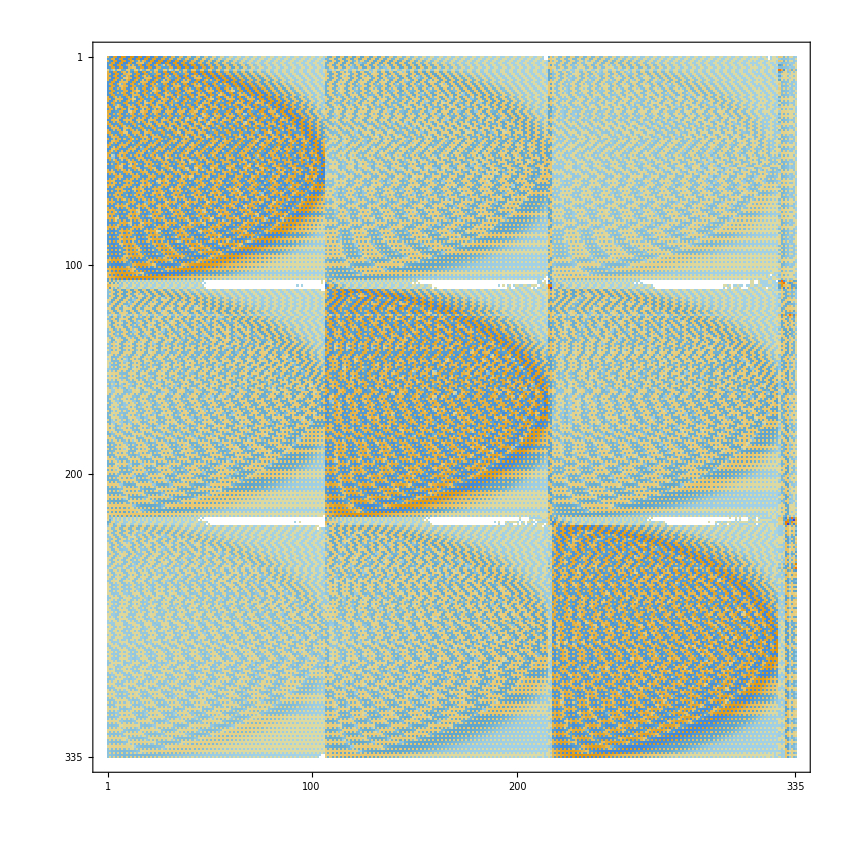

```mathematica
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];

Bfield =0*10^(-4); (* Magnetic field in Tesla *)

Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=100;


For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
EField={0,0,E0};
Temp=Eigenvalues[EI/10^9+BMatrix*Bfield*Subscript[μ, B]/h/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;
Temp2 = Eigenvectors[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9];
For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ] ;

MPList
MatrixPlot[Temp2]
ListPlot[Temp2[[112]],PlotRange->All]
```

```mathematica
LabelList[[112]]
```

60|0|1/2|1/2

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList;
```

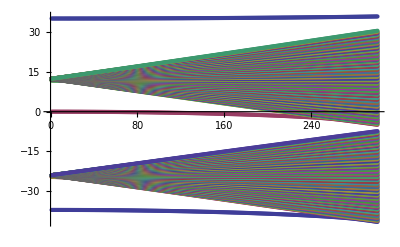

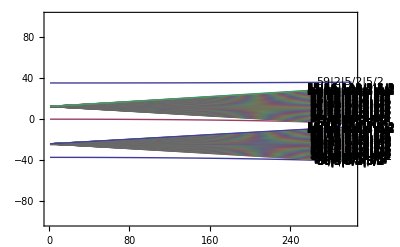

```mathematica
ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

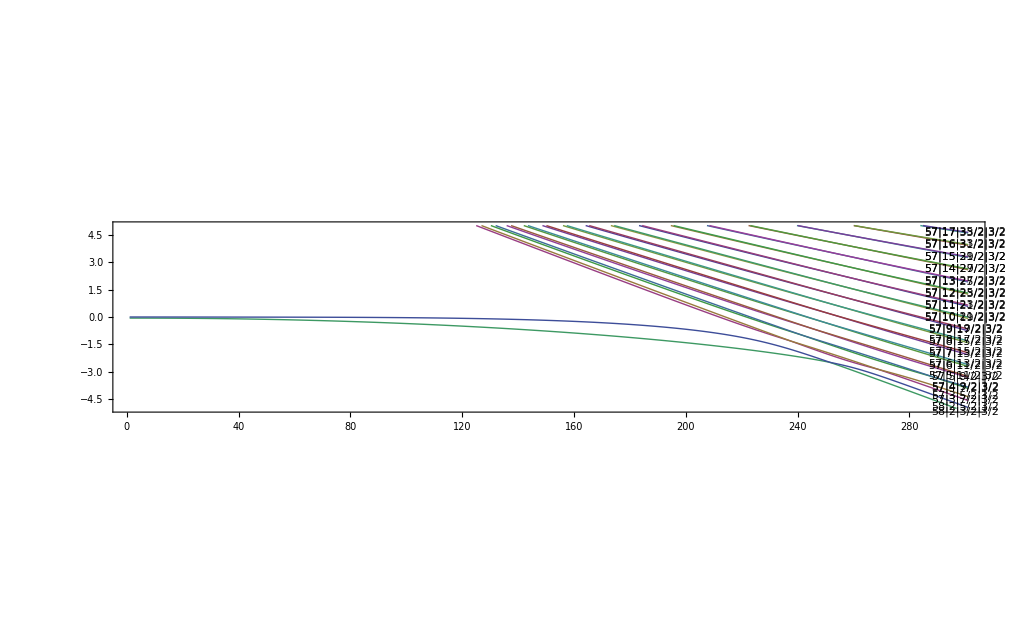

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-5,5}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

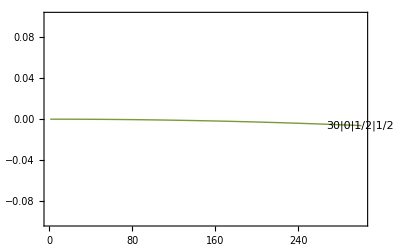

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-0.1,0.1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[105]]
LabelList
```

30|0|1/2|1/2

{27|1|1/2|1/2,27|1|3/2|1/2,26|2|3/2|1/2,26|2|5/2|1/2,28|0|1/2|1/2,25|3|7/2|1/2,25|3|5/2|1/2,25|4|7/2|1/2,25|4|9/2|1/2,25|5|9/2|1/2,25|5|11/2|1/2,25|6|11/2|1/2,25|6|13/2|1/2,25|7|13/2|1/2,25|7|15/2|1/2,25|8|15/2|1/2,25|8|17/2|1/2,25|9|17/2|1/2,25|9|19/2|1/2,25|10|19/2|1/2,25|10|21/2|1/2,25|11|21/2|1/2,25|11|23/2|1/2,25|12|23/2|1/2,25|12|25/2|1/2,25|13|25/2|1/2,25|13|27/2|1/2,25|14|27/2|1/2,25|14|29/2|1/2,25|15|29/2|1/2,25|15|31/2|1/2,25|16|31/2|1/2,25|16|33/2|1/2,25|17|33/2|1/2,25|17|35/2|1/2,25|18|35/2|1/2,25|18|37/2|1/2,25|19|37/2|1/2,25|19|39/2|1/2,25|20|39/2|1/2,25|20|41/2|1/2,25|21|41/2|1/2,25|21|43/2|1/2,25|22|43/2|1/2,25|22|45/2|1/2,25|23|45/2|1/2,25|23|47/2|1/2,25|24|47/2|1/2,25|24|49/2|1/2,28|1|1/2|1/2,28|1|3/2|1/2,27|2|3/2|1/2,27|2|5/2|1/2,29|0|1/2|1/2,26|3|7/2|1/2,26|3|5/2|1/2,26|4|7/2|1/2,26|4|9/2|1/2,26|5|9/2|1/2,26|5|11/2|1/2,26|6|11/2|1/2,26|6|13/2|1/2,26|7|13/2|1/2,26|7|15/2|1/2,26|8|15/2|1/2,26|8|17/2|1/2,26|9|17/2|1/2,26|9|19/2|1/2,26|10|19/2|1/2,26|10|21/2|1/2,26|11|21/2|1/2,26|11|23/2|1/2,26|12|23/2|1/2,26|12|25/2|1/2,26|13|25/2|1/2,26|13|27/2|1/2,26|14|27/2|1/2,26|14|29/2|1/2,26|15|29/2|1/2,26|15|31/2|1/2,26|16|31/2|1/2,26|16|33/2|1/2,26|17|33/2|1/2,26|17|35/2|1/2,26|18|35/2|1/2,26|18|37/2|1/2,26|19|37/2|1/2,26|19|39/2|1/2,26|20|39/2|1/2,26|20|41/2|1/2,26|21|41/2|1/2,26|21|43/2|1/2,26|22|43/2|1/2,26|22|45/2|1/2,26|23|45/2|1/2,26|23|47/2|1/2,26|24|47/2|1/2,26|24|49/2|1/2,26|25|49/2|1/2,26|25|51/2|1/2,29|1|1/2|1/2,29|1|3/2|1/2,28|2|3/2|1/2,28|2|5/2|1/2,30|0|1/2|1/2,27|3|7/2|1/2,27|3|5/2|1/2,27|4|7/2|1/2,27|4|9/2|1/2,27|5|9/2|1/2,27|5|11/2|1/2,27|6|11/2|1/2,27|6|13/2|1/2,27|7|13/2|1/2,27|7|15/2|1/2,27|8|15/2|1/2,27|8|17/2|1/2,27|9|17/2|1/2,27|9|19/2|1/2,27|10|19/2|1/2,27|10|21/2|1/2,27|11|21/2|1/2,27|11|23/2|1/2,27|12|23/2|1/2,27|12|25/2|1/2,27|13|25/2|1/2,27|13|27/2|1/2,27|14|27/2|1/2,27|14|29/2|1/2,27|15|29/2|1/2,27|15|31/2|1/2,27|16|31/2|1/2,27|16|33/2|1/2,27|17|33/2|1/2,27|17|35/2|1/2,27|18|35/2|1/2,27|18|37/2|1/2,27|19|37/2|1/2,27|19|39/2|1/2,27|20|39/2|1/2,27|20|41/2|1/2,27|21|41/2|1/2,27|21|43/2|1/2,27|22|43/2|1/2,27|22|45/2|1/2,27|23|45/2|1/2,27|23|47/2|1/2,27|24|47/2|1/2,27|24|49/2|1/2,27|25|49/2|1/2,27|25|51/2|1/2,27|26|51/2|1/2,27|26|53/2|1/2,30|1|1/2|1/2,30|1|3/2|1/2,29|2|3/2|1/2,29|2|5/2|1/2,31|0|1/2|1/2,28|3|7/2|1/2,28|3|5/2|1/2,28|4|7/2|1/2,28|4|9/2|1/2,28|5|9/2|1/2,28|5|11/2|1/2,28|6|11/2|1/2,28|6|13/2|1/2,28|7|13/2|1/2,28|7|15/2|1/2,28|8|15/2|1/2,28|8|17/2|1/2,28|9|17/2|1/2,28|9|19/2|1/2,28|10|19/2|1/2,28|10|21/2|1/2,28|11|21/2|1/2,28|11|23/2|1/2,28|12|23/2|1/2,28|12|25/2|1/2,28|13|25/2|1/2,28|13|27/2|1/2,28|14|27/2|1/2,28|14|29/2|1/2,28|15|29/2|1/2,28|15|31/2|1/2,28|16|31/2|1/2,28|16|33/2|1/2,28|17|33/2|1/2,28|17|35/2|1/2,28|18|35/2|1/2,28|18|37/2|1/2,28|19|37/2|1/2,28|19|39/2|1/2,28|20|39/2|1/2,28|20|41/2|1/2,28|21|41/2|1/2,28|21|43/2|1/2,28|22|43/2|1/2,28|22|45/2|1/2,28|23|45/2|1/2,28|23|47/2|1/2,28|24|47/2|1/2,28|24|49/2|1/2,28|25|49/2|1/2,28|25|51/2|1/2,28|26|51/2|1/2,28|26|53/2|1/2,28|27|53/2|1/2,28|27|55/2|1/2,31|1|1/2|1/2,31|1|3/2|1/2,30|2|3/2|1/2,30|2|5/2|1/2,32|0|1/2|1/2,29|3|7/2|1/2,29|3|5/2|1/2,29|4|7/2|1/2,29|4|9/2|1/2,29|5|9/2|1/2,29|5|11/2|1/2,29|6|11/2|1/2,29|6|13/2|1/2,29|7|13/2|1/2,29|7|15/2|1/2,29|8|15/2|1/2,29|8|17/2|1/2,29|9|17/2|1/2,29|9|19/2|1/2,29|10|19/2|1/2,29|10|21/2|1/2,29|11|21/2|1/2,29|11|23/2|1/2,29|12|23/2|1/2,29|12|25/2|1/2,29|13|25/2|1/2,29|13|27/2|1/2,29|14|27/2|1/2,29|14|29/2|1/2,29|15|29/2|1/2,29|15|31/2|1/2,29|16|31/2|1/2,29|16|33/2|1/2,29|17|33/2|1/2,29|17|35/2|1/2,29|18|35/2|1/2,29|18|37/2|1/2,29|19|37/2|1/2,29|19|39/2|1/2,29|20|39/2|1/2,29|20|41/2|1/2,29|21|41/2|1/2,29|21|43/2|1/2,29|22|43/2|1/2,29|22|45/2|1/2,29|23|45/2|1/2,29|23|47/2|1/2,29|24|47/2|1/2,29|24|49/2|1/2,29|25|49/2|1/2,29|25|51/2|1/2,29|26|51/2|1/2,29|26|53/2|1/2,29|27|53/2|1/2,29|27|55/2|1/2,29|28|55/2|1/2,29|28|57/2|1/2,32|1|1/2|1/2,32|1|3/2|1/2,31|2|3/2|1/2,31|2|5/2|1/2,33|0|1/2|1/2,30|3|7/2|1/2,30|3|5/2|1/2,30|4|7/2|1/2,30|4|9/2|1/2,30|5|9/2|1/2,30|5|11/2|1/2,30|6|11/2|1/2,30|6|13/2|1/2,30|7|13/2|1/2,30|7|15/2|1/2,30|8|15/2|1/2,30|8|17/2|1/2,30|9|17/2|1/2,30|9|19/2|1/2,30|10|19/2|1/2,30|10|21/2|1/2,30|11|21/2|1/2,30|11|23/2|1/2,30|12|23/2|1/2,30|12|25/2|1/2,30|13|25/2|1/2,30|13|27/2|1/2,30|14|27/2|1/2,30|14|29/2|1/2,30|15|29/2|1/2,30|15|31/2|1/2,30|16|31/2|1/2,30|16|33/2|1/2,30|17|33/2|1/2,30|17|35/2|1/2,30|18|35/2|1/2,30|18|37/2|1/2,30|19|37/2|1/2,30|19|39/2|1/2,30|20|39/2|1/2,30|20|41/2|1/2,30|21|41/2|1/2,30|21|43/2|1/2,30|22|43/2|1/2,30|22|45/2|1/2,30|23|45/2|1/2,30|23|47/2|1/2,30|24|47/2|1/2,30|24|49/2|1/2,30|25|49/2|1/2,30|25|51/2|1/2,30|26|51/2|1/2,30|26|53/2|1/2,30|27|53/2|1/2,30|27|55/2|1/2,30|28|55/2|1/2,30|28|57/2|1/2,30|29|57/2|1/2,30|29|59/2|1/2,33|1|1/2|1/2,33|1|3/2|1/2}

```mathematica
MPList[[105]]

Export["30s_stark_Shift.dat",MPList[[105]]]
```

{{1,-6.89943×10^-8},{2,-2.75954×10^-7},{3,-6.20919×10^-7},{4,-1.10384×10^-6},{5,-1.72476×10^-6},{6,-2.48366×10^-6},{7,-3.38054×10^-6},{8,-4.41539×10^-6},{9,-5.58823×10^-6},{10,-6.89905×10^-6},{11,-8.34786×10^-6},{12,-9.93464×10^-6},{13,-0.0000116594},{14,-0.0000135221},{15,-0.0000155229},{16,-0.0000176616},{17,-0.0000199383},{18,-0.0000223529},{19,-0.0000249056},{20,-0.0000275962},{21,-0.0000304248},{22,-0.0000333914},{23,-0.000036496},{24,-0.0000397386},{25,-0.0000431191},{26,-0.0000466376},{27,-0.0000502941},{28,-0.0000540886},{29,-0.0000580211},{30,-0.0000620915},{31,-0.0000663},{32,-0.0000706464},{33,-0.0000751308},{34,-0.0000797532},{35,-0.0000845135},{36,-0.0000894119},{37,-0.0000944482},{38,-0.0000996225},{39,-0.000104935},{40,-0.000110385},{41,-0.000115973},{42,-0.0001217},{43,-0.000127564},{44,-0.000133566},{45,-0.000139706},{46,-0.000145984},{47,-0.000152401},{48,-0.000158955},{49,-0.000165647},{50,-0.000172477},{51,-0.000179445},{52,-0.000186551},{53,-0.000193795},{54,-0.000201177},{55,-0.000208697},{56,-0.000216355},{57,-0.000224151},{58,-0.000232085},{59,-0.000240157},{60,-0.000248367},{61,-0.000256715},{62,-0.000265201},{63,-0.000273825},{64,-0.000282587},{65,-0.000291487},{66,-0.000300524},{67,-0.0003097},{68,-0.000319014},{69,-0.000328466},{70,-0.000338056},{71,-0.000347784},{72,-0.000357649},{73,-0.000367653},{74,-0.000377795},{75,-0.000388075},{76,-0.000398492},{77,-0.000409048},{78,-0.000419742},{79,-0.000430574},{80,-0.000441543},{81,-0.000452651},{82,-0.000463897},{83,-0.00047528},{84,-0.000486802},{85,-0.000498461},{86,-0.000510259},{87,-0.000522195},{88,-0.000534268},{89,-0.00054648},{90,-0.000558829},{91,-0.000571317},{92,-0.000583943},{93,-0.000596706},{94,-0.000609608},{95,-0.000622647},{96,-0.000635825},{97,-0.00064914},{98,-0.000662594},{99,-0.000676185},{100,-0.000689915},{101,-0.000703782},{102,-0.000717788},{103,-0.000731931},{104,-0.000746213},{105,-0.000760632},{106,-0.00077519},{107,-0.000789885},{108,-0.000804719},{109,-0.00081969},{110,-0.000834799},{111,-0.000850047},{112,-0.000865432},{113,-0.000880956},{114,-0.000896617},{115,-0.000912417},{116,-0.000928354},{117,-0.000944429},{118,-0.000960643},{119,-0.000976994},{120,-0.000993484},{121,-0.00101011},{122,-0.00102688},{123,-0.00104378},{124,-0.00106082},{125,-0.001078},{126,-0.00109532},{127,-0.00111277},{128,-0.00113037},{129,-0.0011481},{130,-0.00116597},{131,-0.00118397},{132,-0.00120212},{133,-0.0012204},{134,-0.00123882},{135,-0.00125738},{136,-0.00127608},{137,-0.00129492},{138,-0.00131389},{139,-0.001333},{140,-0.00135225},{141,-0.00137164},{142,-0.00139116},{143,-0.00141083},{144,-0.00143063},{145,-0.00145057},{146,-0.00147065},{147,-0.00149086},{148,-0.00151121},{149,-0.00153171},{150,-0.00155234},{151,-0.0015731},{152,-0.00159401},{153,-0.00161505},{154,-0.00163623},{155,-0.00165755},{156,-0.00167901},{157,-0.00170061},{158,-0.00172234},{159,-0.00174421},{160,-0.00176622},{161,-0.00178837},{162,-0.00181065},{163,-0.00183308},{164,-0.00185564},{165,-0.00187834},{166,-0.00190118},{167,-0.00192415},{168,-0.00194727},{169,-0.00197052},{170,-0.00199391},{171,-0.00201743},{172,-0.0020411},{173,-0.0020649},{174,-0.00208885},{175,-0.00211293},{176,-0.00213714},{177,-0.0021615},{178,-0.00218599},{179,-0.00221063},{180,-0.00223539},{181,-0.0022603},{182,-0.00228535},{183,-0.00231053},{184,-0.00233585},{185,-0.00236131},{186,-0.00238691},{187,-0.00241265},{188,-0.00243852},{189,-0.00246453},{190,-0.00249068},{191,-0.00251697},{192,-0.0025434},{193,-0.00256996},{194,-0.00259667},{195,-0.00262351},{196,-0.00265048},{197,-0.0026776},{198,-0.00270485},{199,-0.00273225},{200,-0.00275978},{201,-0.00278744},{202,-0.00281525},{203,-0.0028432},{204,-0.00287128},{205,-0.0028995},{206,-0.00292786},{207,-0.00295635},{208,-0.00298499},{209,-0.00301376},{210,-0.00304267},{211,-0.00307172},{212,-0.00310091},{213,-0.00313023},{214,-0.00315969},{215,-0.00318929},{216,-0.00321903},{217,-0.00324891},{218,-0.00327893},{219,-0.00330908},{220,-0.00333937},{221,-0.0033698},{222,-0.00340037},{223,-0.00343107},{224,-0.00346191},{225,-0.00349289},{226,-0.00352401},{227,-0.00355527},{228,-0.00358667},{229,-0.0036182},{230,-0.00364987},{231,-0.00368168},{232,-0.00371363},{233,-0.00374571},{234,-0.00377794},{235,-0.0038103},{236,-0.0038428},{237,-0.00387544},{238,-0.00390821},{239,-0.00394113},{240,-0.00397418},{241,-0.00400737},{242,-0.0040407},{243,-0.00407416},{244,-0.00410777},{245,-0.00414151},{246,-0.00417539},{247,-0.00420941},{248,-0.00424356},{249,-0.00427786},{250,-0.00431229},{251,-0.00434686},{252,-0.00438157},{253,-0.00441641},{254,-0.0044514},{255,-0.00448652},{256,-0.00452178},{257,-0.00455718},{258,-0.00459272},{259,-0.00462839},{260,-0.0046642},{261,-0.00470016},{262,-0.00473624},{263,-0.00477247},{264,-0.00480884},{265,-0.00484534},{266,-0.00488198},{267,-0.00491876},{268,-0.00495568},{269,-0.00499273},{270,-0.00502993},{271,-0.00506726},{272,-0.00510473},{273,-0.00514234},{274,-0.00518008},{275,-0.00521797},{276,-0.00525599},{277,-0.00529415},{278,-0.00533245},{279,-0.00537088},{280,-0.00540946},{281,-0.00544817},{282,-0.00548702},{283,-0.00552601},{284,-0.00556513},{285,-0.0056044},{286,-0.0056438},{287,-0.00568334},{288,-0.00572302},{289,-0.00576284},{290,-0.00580279},{291,-0.00584289},{292,-0.00588312},{293,-0.00592349},{294,-0.00596399},{295,-0.00600464},{296,-0.00604542},{297,-0.00608634},{298,-0.0061274},{299,-0.0061686},{300,-0.00620994},{301,-0.00625141}}

30s_stark_Shift.dat

```mathematica
(*Export data for Origin*)
Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=MPList[[i,j,2]] 
 ]
] ;

MPListExport



Export["Stark_Shifts_around_60s.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_60s.dat",Efieldlist]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{«1»}

Stark_Shifts_around_60s.dat

Electric_fields_for_Stark_Shifts_around_60s.dat

```mathematica
⁃Graphics⁃⁃Graphics⁃ n=15 -18, ninitial=15, Subscript[m, j]=1/2
```

⁃Graphics⁃

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃ n=15-17 , Subscript[m, j]=5/2, n initial=15.
```

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p, EField =(0,0,E0)
```

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 350 level, n=41 to 47, M=1
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E in V/m, 147 level, n=42 to 46, M=1
```